```mathematica
(*css zebrafinch model*)
ns := Na ba pa + Nn bn pn;
nh:= Na ba (1-pa) + Nn bn (1-pn);
NNa :=ns vs((1-lsO) vI z +lsO qO ) + nh vh((1-lhO) vI z +lhO qO );
NNn :=ns vs((1-lsO) vI (1-z)+lsO(1- qO) ) + nh vh((1-lhO) vI (1-z)+lhO(1- qO) );
qO := (1-u)(Na/(Na +Nn));
(*leave Q in matrix below different than one up above recursions*)
```

```mathematica
AA:=({{0, 0, ba pa, bn pn}, {0, 0, ba(1-pa), bn(1-pn)}, {vs((1-lsO) vI z +lsO Qh), vh((1-lhO) vI z +lhO Qh ), 0, 0}, {vs((1-lsO) vI (1-z)+lsO(1- Qh) ), vh((1-lhO) vI (1-z)+lhO(1- Qh) ), 0, 0}})
```

```mathematica
NN = FullSimplify[NNn + NNa];
```

```mathematica
FFa=FullSimplify[NNa/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
FFn=FullSimplify[NNn/NN/.{Na->Fa N0,Nn->(1-Fa)N0}];
```

```mathematica
Simplify[FFn+FFa]
```

1

```mathematica
(* identify Q-hat for common strategy*)
Fasols=Solve[FFa==Fa,Fa];
```

{1.2,1.5,2,3,5}

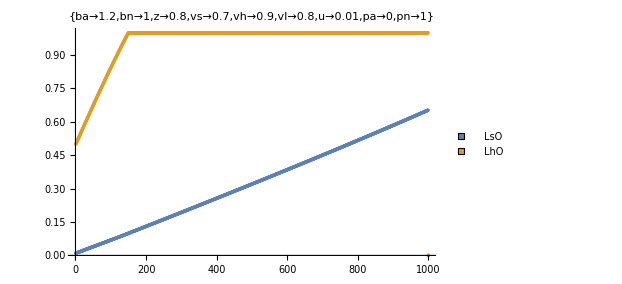

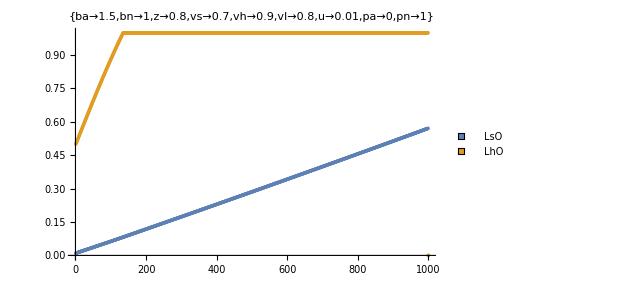

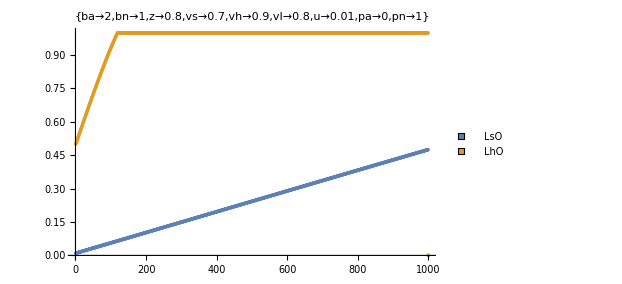

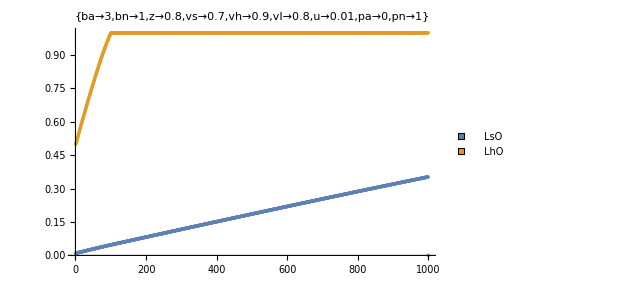

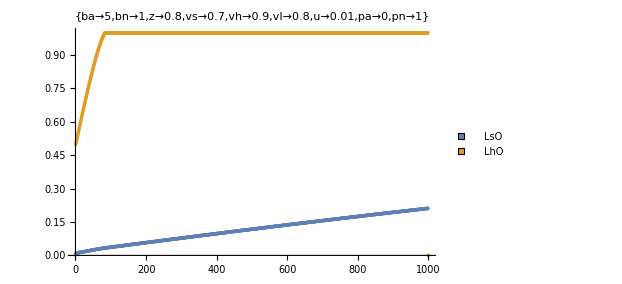

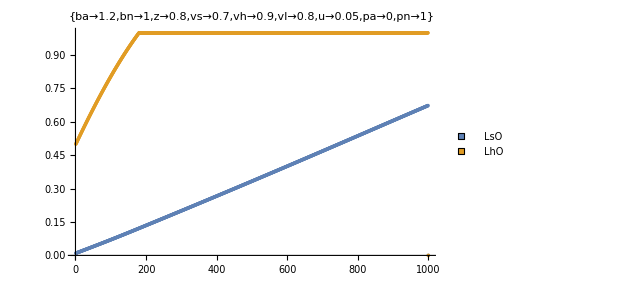

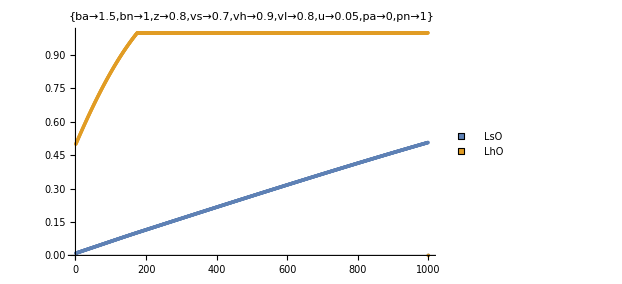

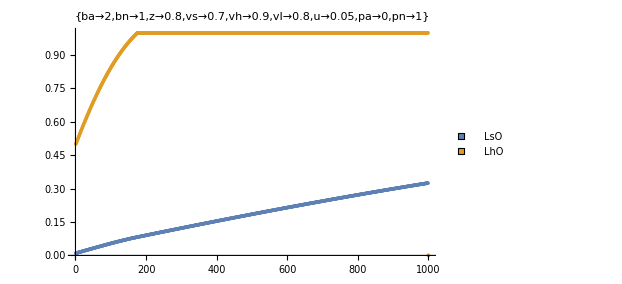

```mathematica
(* begin looping here*)
ulist={0.01,0.05,0.1, 0.2 , 0.4};
blist={1.2,1.5,2,3,5}
lsOstart=0.01;
lhOstart=0.5;
imax=1000;
For[h=1,h≤5,h++,{
For[j=1,j≤5,j++,{
subs = {ba->blist[[j]],bn->1,z->.8,vs->.7,vh->.9,vI->.8  ,u->ulist[[h]] , pa -> 0, pn-> 1};
test = {lsO->0 ,lsV-> 0 ,lsI-> 0.8,lhO-> 0.8,lhI-> 0.2};
QHAT[LHO_,LSO_] :=Simplify[Fasols[[1,1,2]]/.{lhO->LHO,lhI -> LHI, lsO -> LSO, lsI-> LSI} /.subs];
(*isolate dominant eigenvalue*)
AA2=AA/.subs;
LL=Eigenvalues[AA2];
(*isolate Dominant eigenvalue, substitute in q-hat *)
Lambda1[ lsO_, lhO_,LHO_,LSO_]:= Simplify[LL[[2]]/.Qh->  QHAT[LHO,LSO]];
(*take partial derivatives to calculate gradient, substitute mutant for common type*)
DlsO=D[Lambda1[lsO, lhO,LHO,LSO],lsO]/. {LHO -> lhO,LSO-> lsO};
DlhO=D[Lambda1[lsO, lhO,LHO,LSO],lhO]/. {LHO -> lhO,LSO-> lsO};
(*try and graph*)
lsOtab=Table[0,{i,imax}];
lhOtab=Table[0,{i,imax}];
DlsOtab=Table[0,{i,imax}];
DlhOtab=Table[0,{i,imax}];
delta=0.04;
lsOtab[[1]]=lsOstart;
lhOtab[[1]]=lhOstart;
DlsOtab[[1]]=DlsO/.subs/.{lsO->lsOstart,lhO->lhOstart};
DlhOtab[[1]]=DlhO/.subs/.{lsO->lsOstart,lhO->lhOstart};
For[i=2,i<imax,i++,{

lsOtab[[i]]=lsOtab[[i-1]]  + delta DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lsOtab[[i]]=If[lsOtab[[i]]>1,1,lsOtab[[i]]];
lsOtab[[i]]=If[lsOtab[[i]]<0,0,lsOtab[[i]]];

lhOtab[[i]]=lhOtab[[i-1]]  + delta DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
lhOtab[[i]]=If[lhOtab[[i]]>1,1,lhOtab[[i]]];
lhOtab[[i]]=If[lhOtab[[i]]<0,0,lhOtab[[i]]];

DlsOtab[[i]]=DlsO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
DlhOtab[[i]]=DlhO/.subs/.{lsO->lsOtab[[i-1]],lhO->lhOtab[[i-1]]};
}];

Print[ListPlot[{lsOtab,lhOtab},PlotRange->{All,{0,1}},PlotLegends->PointLegend[{LsO,LhO},LegendMarkers->Graphics[Rectangle[]]],PlotLabel->subs, ImageSize->460]];
}]
}];
```